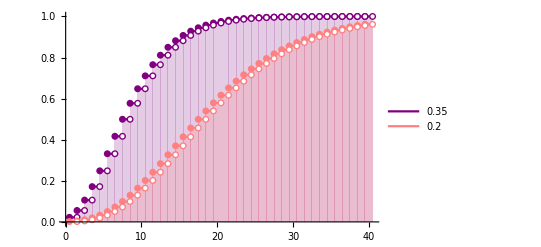

```mathematica
DiscretePlot[Table[CDF[NegativeBinomialDistribution[5,p],k],{p,{0.35, 0.2}}]//Evaluate,{k,40},ExtentSize->Full,ExtentMarkers->{"Filled","Empty"},PlotStyle->{Purple, Pink}, PlotLegends->{0.35,0.2}]
```

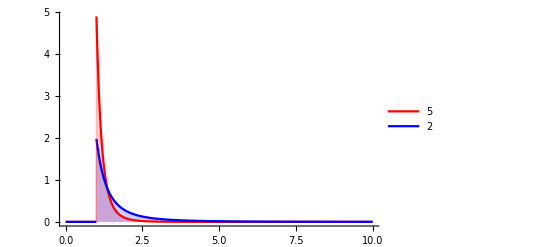

```mathematica
Plot[Table[PDF[ParetoDistribution[1,α],x],{α,{5, 2}}]//Evaluate,{x,0,10},Filling->Axis, PlotRange->All,PlotLegends->{5,2}, PlotStyle->{Red,Blue}]
```

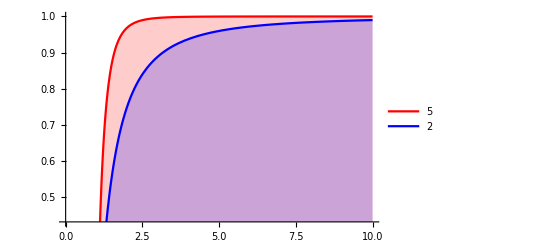

```mathematica
Plot[Table[CDF[ParetoDistribution[1,α],x],{α,{5,2}}]//Evaluate,{x,0,10},Filling->Axis,PlotLegends->{5,2}, PlotStyle->{Red,Blue}]
```

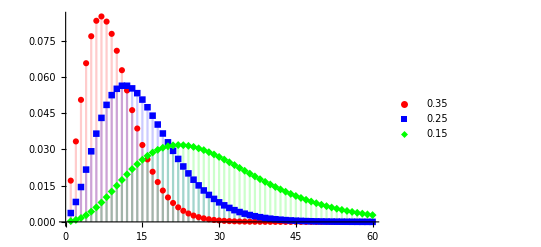

```mathematica
DiscretePlot[Table[PDF[NegativeBinomialDistribution[5,p],k],{p,{0.35, 0.25, 0.15}}]//Evaluate,{k,60},PlotMarkers->Automatic, PlotLegends->{0.35,0.25,0.15}, PlotStyle->{Red,Blue,Green}]
```